# Netbotz data plots Reads Netbotz text files

http : // www4.rcf.bnl.gov/~hneal/NetBotzData.txt

Execute the next expression to input the most recent Netbotz file from the server

```mathematica
infile=URLExecute["http://www4.rcf.bnl.gov/~hneal/NetBotzData.txt"];
```

```mathematica
fileinfull="NetBotzData.txt"
fileinroot=FileBaseName[fileinfull]
fileinS=fileinroot;filein=fileinS;
```

NetBotzData.txt

NetBotzData

```mathematica
infile[[2]]
```

{Thu Feb  5 22:03:01 EST 2015 NetBotzRackMonitor450,EthernetLinkStatus=Up,A-LinkBusPower=OK,SensorPod,DewPoint=33.980000,Humidity=29.000000,Temperature=67.460000,SensorPod9268414,Particles=3.000000,DewPoint=38.300000,Audio=1.000000,AirFlow=0.000000,Humidity=32.000000,Temperature=69.440000,CameraPod9180293,Speakers=Notconnected,ExternalMic=Notconnected,CameraMotion=NoMotion,DoorSwitch=N/A,}

```mathematica
datain=infile;
```

```mathematica
datain[[1]]//TableForm
```

Thu Feb  5 21:53:01 EST 2015 NetBotzRackMonitor450
EthernetLinkStatus=Up
A-LinkBusPower=OK
SensorPod
DewPoint=47.660000
Humidity=49.000000
Temperature=67.640000
SensorPod9268414
Particles=3.000000
DewPoint=51.440000
Audio=1.000000
AirFlow=0.000000
Humidity=56.000000
Temperature=68.000000
CameraPod9180293
Speakers=Notconnected
ExternalMic=Notconnected
CameraMotion=NoMotion
DoorSwitch=N/A

Execute this section to input Netbotz file that has already been downloaded to this computer.

```mathematica
filepathfull = "/Users/takacs/Desktop/NetBotzData.txt";
```

```mathematica
filepathfull=Input["Enter full path to Netbotz text file",filepathfull]
```

$Canceled

```mathematica
SetDirectory[DirectoryName[filepathfull]]
```

SetDirectory[DirectoryName[$Canceled]]

```mathematica
fnames=FileNames["*.txt"];Table[{i,fnames[[i]]},{i,Length[fnames]}]//TableForm
```

1 | BPRAlist1000.txt
2 | idealGauss.txt
3 | MetroLog.txt
4 | sampledGauss.txt
5 | temp.txt

```mathematica
nf=Input["Enter index of file desired",nf]
```

```mathematica
fileinfull =fnames[[nf]]
fileinroot=FileBaseName[fileinfull]
fileinS=fileinroot;filein=fileinS;
```

NetBotzData.txt

NetBotzData

```mathematica
(*Read in raw data here*)
datain=Import[fileinfull,"Lines"];
```

```mathematica
datain[[1]]//TableForm
```

Thu Feb  5 21:53:01 EST 2015 NetBotzRackMonitor450,EthernetLinkStatus=Up,A-LinkBusPower=OK,SensorPod,DewPoint=47.660000,Humidity=49.000000,Temperature=67.640000,SensorPod9268414,Particles=3.000000,DewPoint=51.440000,Audio=1.000000,AirFlow=0.000000,Humidity=56.000000,Temperature=68.000000,CameraPod9180293,Speakers=Notconnected,ExternalMic=Notconnected,CameraMotion=NoMotion,DoorSwitch=N/A,

#### Continue here after file input

Clean up uneven length records

```mathematica
{datain[[1]],datain[[-1]]}//TableForm
```

Thu Feb  5 21:53:01 EST 2015 NetBotzRackMonitor450 | EthernetLinkStatus=Up | A-LinkBusPower=OK | SensorPod | DewPoint=47.660000 | Humidity=49.000000 | Temperature=67.640000 | SensorPod9268414 | Particles=3.000000 | DewPoint=51.440000 | Audio=1.000000 | AirFlow=0.000000 | Humidity=56.000000 | Temperature=68.000000 | CameraPod9180293 | Speakers=Notconnected | ExternalMic=Notconnected | CameraMotion=NoMotion | DoorSwitch=N/A |  | 
Wed Mar 25 12:03:01 EDT 2015 NetBotzRackMonitor450 | EthernetLinkStatus=Up | A-LinkBusPower=OK | SensorPod | DewPoint=48.020000 | Humidity=44.000000 | Temperature=71.240000 | SensorPod9268414 | Particles=3.000000 | Particles=3.000000 | DewPoint=50.360000 | Audio=1.000000 | AirFlow=0.000000 | Humidity=45.000000 | Temperature=73.040000 | CameraPod9180293 | Speakers=Notconnected | ExternalMic=Notconnected | CameraMotion=NoMotion | DoorSwitch=N/A |

```mathematica
datain[[-1,15]]
```

Temperature=73.040000

```mathematica
Length[datain[[-1]]]
```

21

```mathematica
mlen=Map[Length[#]&,datain];
```

```mathematica
mlen[[3]]
```

20

```mathematica
Tally[mlen]
```

{{20,1896},{1,5},{21,2665}}

```mathematica
datain2=Map[StringSplit[#,","]&,datain];
```

```mathematica
datain2//Length
```

4566

```mathematica
datain2[[-2;;-1]]
```

{{{Wed Mar 25 11:48:01 EDT 2015 NetBotzRackMonitor450},{EthernetLinkStatus=Up},{A-LinkBusPower=OK},{SensorPod},{DewPoint=35.240000},{Humidity=27.000000},{Temperature=71.060000},{SensorPod9268414},{Particles=3.000000},{Particles=3.000000},{DewPoint=40.640000},{Audio=1.000000},{AirFlow=0.000000},{Humidity=31.000000},{Temperature=73.220000},{CameraPod9180293},{Speakers=Notconnected},{ExternalMic=Notconnected},{CameraMotion=NoMotion},{DoorSwitch=N/A},{}},{{Wed Mar 25 12:03:01 EDT 2015 NetBotzRackMonitor450},{EthernetLinkStatus=Up},{A-LinkBusPower=OK},{SensorPod},{DewPoint=48.020000},{Humidity=44.000000},{Temperature=71.240000},{SensorPod9268414},{Particles=3.000000},{Particles=3.000000},{DewPoint=50.360000},{Audio=1.000000},{AirFlow=0.000000},{Humidity=45.000000},{Temperature=73.040000},{CameraPod9180293},{Speakers=Notconnected},{ExternalMic=Notconnected},{CameraMotion=NoMotion},{DoorSwitch=N/A},{}}}

One of the records is short, so it kills the output. Need to check record length.

```mathematica
dat=Reap[Do[
If[Length[datain2[[i]]]==20,Sow[{Take[datain2[[i]],{1}],Take[datain2[[i]],{7}],Take[datain2[[i]],{14}]}//Flatten]];
If[Length[datain2[[i]]]==21,Sow[{Take[datain2[[i]],{1}],Take[datain2[[i]],{7}],Take[datain2[[i]],{15}]}//Flatten]]

,{i,Length[datain2]}]];
dat=Flatten[Drop[dat,1],2];(*Get rid of the Null at the front*)
```

```mathematica
dat[[-1]]
```

{Wed Mar 25 12:03:01 EDT 2015 NetBotzRackMonitor450,Temperature=71.240000,Temperature=73.040000}

```mathematica
dat[[1,1]]
```

Thu Feb  5 21:53:01 EST 2015 NetBotzRackMonitor450

```mathematica
StringDrop[dat[[1,1]],{-22,-1}]
```

Thu Feb  5 21:53:01 EST 2015

```mathematica
dropf[listel_]:={StringDrop[Take[listel,1],{-22,-1}],StringDrop[Take[listel,{2}],12],StringDrop[Take[listel,{3}],12]}//Flatten
```

```mathematica
dat2=Map[dropf[#]&,dat];
```

```mathematica
dat2[[1;;3]]
```

{{Thu Feb  5 21:53:01 EST 2015,67.640000,68.000000},{Thu Feb  5 22:03:01 EST 2015,67.460000,69.440000},{Thu Feb  5 22:18:01 EST 2015,67.640000,69.440000}}

```mathematica
dat2[[-100;;-1,1]];
```

```mathematica
DateString[dat2[[1,1]],"DateTime"]
```

Thursday 5 February 2015 21:53:01

```mathematica
AbsoluteTime[dat2[[1,1]]]
```

3632161981

Set default pts here

```mathematica
offsetFromEnd=0;
npts=600;
```

Iterate to tune the plot from here

```mathematica
{npts,offsetFromEnd}=Input["Enter npts and offset from end",{npts,offsetFromEnd} ]
```

{200,0}

```mathematica
temp=.;
```

```mathematica
time=Take[dat2,All,1][[-offsetFromEnd-npts;;-1-offsetFromEnd]]//Flatten;
```

```mathematica
Temp1=Take[dat2,All,{2}][[-offsetFromEnd-npts;;-1-offsetFromEnd]]//Flatten//ToExpression;
```

```mathematica
Temp2=Take[dat2,All,{3}][[-offsetFromEnd-npts;;-1-offsetFromEnd]]//Flatten//ToExpression;
```

```mathematica
(*temp1=Map[AbsoluteTime[#]&,Take[dat2,All,1][[1;;10]]//Flatten]*)
```

```mathematica
temp2=Take[dat2,All,{2}][[-100;;-1]]//Flatten//ToExpression;
```

```mathematica
timetemp1=Transpose[{time,Temp1}];
```

```mathematica
timetemp2=Transpose[{time,Temp2}];
```

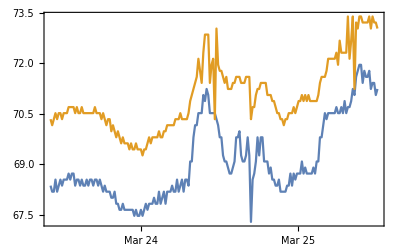

```mathematica
dlplot=DateListPlot[{timetemp1,timetemp2}]
```

```mathematica
filepath=Input["Input Filepath to desired directory",filepath]
```

filepath

```mathematica
Button["Export Temp plot",SetDirectory[DirectoryName[filepath,1]];Export["RoomTemp_"<>ToString[npts]<>"_"<>ToString[offsetFromEnd]<>".tiff",dlplot,"ImageEncoding"->"LZW",ImageResolution->100];ResetDirectory[],Method->"Queued"]
```

Export Temp plot